```mathematica
SetDirectory[NotebookDirectory[]];
nff[Eq_,T_,μ_]:=If[(Eq-μ)/T>60.,0.,1/(Exp[(Eq-μ)/T]+1)];
nfa[Eq_,T_,μ_]:=If[(Eq+μ)/T>60.,0.,1/(Exp[(Eq+μ)/T]+1)];
mf2[h_,ρ_]:=(h^2 ρ)/2;
Nf=2;
Nc=3;
h=6.5;
λ300=75.8;
ν300=-482.^2;
Λ=5000.;
Fmass[sigma_,h_,T_,mu_]:=-(2 h^2 Nc)/(2 π^2) NIntegrate[q^2/(2 √(q^2+mf2[h,sigma^2/2]))(0.-nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu]),{q,0.,500.,5000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5];
F0[omega_,ps_,sigma_,h_,T_,mu_]:=If[omega<√(4*mf2[h,sigma^2/2]+ps^2),0.,If[√(4*mf2[h,sigma^2/2]+ps^2)<omega<√mf2[h,sigma^2/2]+√(mf2[h,sigma^2/2]+ps^2),NIntegrate[-(q(-π))/(4 ps √(q^2+mf2[h,sigma^2/2]))(nff[√(q^2+mf2[h,sigma^2/2])-omega,T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu]),{q,ps/2-1/2 √((4 mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2)),ps/2+1/2 √((4 mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2))},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5],NIntegrate[-(q(-π))/(4ps √(q^2+mf2[h,sigma^2/2]))(nff[√(q^2+mf2[h,sigma^2/2])-omega,T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu]),{q,-ps/2+1/2 √((4mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2)),ps/2+1/2 √((4mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2))},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5]]];
F1[omega_,ps_,sigma_,h_,T_,mu_]:=If[0.<omega<ps,(-omega^2+ps^2)*(h^2 Nc)/(4 π^2)*π/(4ps)NIntegrate[q/(√(q^2+mf2[h,sigma^2/2]))(nfa[√(q^2+mf2[h,sigma^2/2])-omega,T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu]),{q,ps/2+1/2 √((4 mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2)),Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5],0.];
F2[omega_,ps_,sigma_,h_,T_,mu_]:=If[0.<omega<-√mf2[h,sigma^2/2]+√(ps^2+mf2[h,sigma^2/2]),(-omega^2+ps^2)*(h^2 Nc)/(4 π^2)*π/(4ps)NIntegrate[q/(√(q^2+mf2[h,sigma^2/2]))(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+mf2[h,sigma^2/2])+omega,T,mu]),{q,ps/2-1/2 √((4 mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2)),Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5],If[-√mf2[h,sigma^2/2]+√(ps^2+mf2[h,sigma^2/2])<omega<ps,(-omega^2+ps^2)*(h^2 Nc)/(4 π^2)*π/(4ps)NIntegrate[q/(√(q^2+mf2[h,sigma^2/2]))(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+mf2[h,sigma^2/2])+omega,T,mu]),{q,-ps/2+1/2 √((4 mf2[h,sigma^2/2] omega^2+ps^2 omega^2-omega^4)/(ps^2-omega^2)),Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5],0.]];
Imthr[omega_,ps_,sigma_,h_,T_,mu_]:=-(F0[omega,ps,sigma,h,T,mu]+F1[omega,ps,sigma,h,T,mu]+F2[omega,ps,sigma,h,T,mu]);
gammavac[omega_,ps_,ϵ_,sigma_,h_,Mmass_,MZ_,λ_,ν_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,sigma^2/2])/Mmass])mf2[h,sigma^2/2]+((-ⅈ(omega+ⅈ ϵ))^2+ps^2)/2(NIntegrate[Log[1/MZ^2(-((-ⅈ(omega+ⅈ ϵ))^2+ps^2)(x-1)^2-x((-ⅈ(omega+ⅈ ϵ))^2+ps^2)+((-ⅈ(omega+ⅈ ϵ))^2+ps^2)+mf2[h,sigma^2/2])],{x,0,1}]-NIntegrate[Log[1/MZ^2(-((*(-ⅈ(omega+ⅈ ϵ))^2*)+ps^2)(x-1)^2-x((*(-ⅈ(omega+ⅈ ϵ))^2*)+ps^2)+((*(-ⅈ(omega+ⅈ ϵ))^2*)+ps^2)+300.^2)],{x,0,1}]))-(Nc h^2 mf2[h,sigma^2/2])/(16 π^2)+(-ⅈ(omega+ⅈ ϵ))^2+ps^2+(λ sigma^2/2+ν);
Impart[omega_,ps_,ϵ_,sigma_,h_,Mmass_,MZ_,λ_,ν_,T_,mu_]:=Imthr[omega,ps,sigma,h,T,mu]-Im[gammavac[omega,ps,ϵ,sigma,h,Mmass,MZ,λ,ν]];
fpi=16.586579821171867;
```

```mathematica
CloseKernels[];
LaunchKernels[52];
$KernelCount
```

52

```mathematica
Imdata=Table[ParallelTable[Impart[omega,ps,0.,fpi,6.5,300.,300.,λ300,ν300,30.,320.]//Quiet,{omega,1,2001,10}],{ps,0,2000,10}];
```

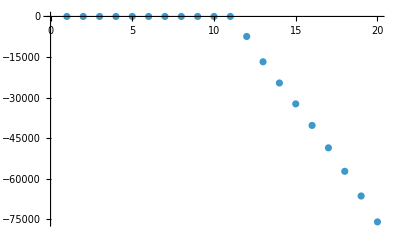

```mathematica
ListPlot[Imdata[[1]][[1;;20]]]
```

```mathematica
Export["./input_data/ImdataT30mu320.dat",Imdata]
```

./input_data/ImdataT30mu320.dat